```mathematica
Manipulate[Plot[{-kk*x(x-1),0.5},{x,0,1}],{kk,0.1,3}]
```

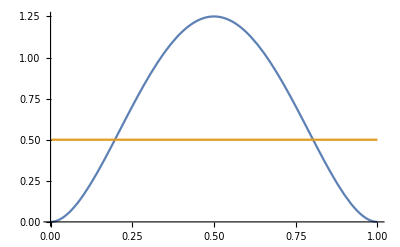

```mathematica
Plot[{20*x^2(x-1)^2,0.5},{x,0,1}]
```

```mathematica
alphaRod = 0.02;
```

```mathematica
valsA = NDSolveValue[{D[u[x,t],t]-alphaRod*Laplacian[u[x,t],{x}]==0,DirichletCondition[u[x,t]==20*x^2*(x-1)^2,t==0]},u,{x,0,1},{t,0,10}]
```

NDSolveValue::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

InterpolatingFunction[{{0., 1.}, {0., 10.}}, <>]

```mathematica
vals = NDSolveValue[{D[u[x,t],t]-alphaRod*Laplacian[u[x,t],{x}]==NeumannValue[0,x==0 || x==1],DirichletCondition[u[x,t]==20*x^2*(x-1)^2,t==0]},u,{x,0,1},{t,0,10}]
```

NDSolveValue::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

InterpolatingFunction[{{0., 1.}, {0., 10.}}, <>]

```mathematica
Manipulate[Plot[{valsA[x,t],0,1.2},{x,0,1}],{t,0,10}]
```

```mathematica
epsilon = 0.1;
```

```mathematica
diff[x_]:=Piecewise[{{0.02, x < 0.5-epsilon},{0.8,x ≥ 0.5-epsilon && x < 0.5 + epsilon},{0.02,x≥0.5+epsilon}}];
```

```mathematica
vals2 = NDSolveValue[{D[u[x,t],t]-diff[x]*Laplacian[u[x,t],{x}]==NeumannValue[0,x==0 || x==1],DirichletCondition[u[x,t]==20*x^2*(x-1)^2,t==0]},u,{x,0,1},{t,0,10}]
```

NDSolveValue::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

InterpolatingFunction[{{0., 1.}, {0., 10.}}, <>]

```mathematica
vals2A = NDSolveValue[{D[u[x,t],t]-diff[x]*Laplacian[u[x,t],{x}]==0,DirichletCondition[u[x,t]==20*x^2*(x-1)^2,t==0]},u,{x,0,1},{t,0,10}]
```

NDSolveValue::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

InterpolatingFunction[{{0., 1.}, {0., 10.}}, <>]

```mathematica
Manipulate[Plot[{vals2A[x,t],valsA[x,t],0,1.2},{x,0,1}],{t,0,10}]
```